```mathematica
func[x_]:=1/(x^2+x);
b = 2;
a=1;
(*
	Замена x-> (b-a)/2 t+(b+a)/2
Pn=1/(2^n n!)*d^n/dx^n[(x^2-1)^n]
*)
pols=Table[Simplify[1/(2^n*n!)*D[(x^2-1)^n,{x,n }]],{n,2,5,1}];
knots=Table[
Solve[pols[[n]]==0,x]
,{n,1,4,1}];
wn=Table[Product[x-knots[[n]][[k]][[1]][[2]],{k,1,n+1}],{n,1,4,1}];
knots[[1]][[1]][[1]][[2]];
Length[knots[[1]]];
coef=Table[
Table[
(NIntegrate[(wn[[n]]/(x-knots[[n]][[i]][[1]][[2]]))^2,{x,-1,1}]//N)/(((wn[[n]]/(x-knots[[n]][[i]][[1]][[2]]))^2)/.{x->knots[[n]][[i]][[1]][[2]]})
,{i,1,Length[knots[[n]]],1}]
,{n,1,4,1}];
Table[(b-a)/2*Sum[coef[[n-1]][[i]]*func[(b-a)/2* knots[[n-1]][[i]][[1]][[2]]+(b+a)/2],{i,1,n,1}],{n,2,5,1}]
Log[4/3]//N
Sum[func[x]*1/1000//N,{x,1,2,1/1000}]
```

{0.286902,0.287657,0.287681,0.287682}

0.287682

0.288015

{1.96784,1.96015,1.95978,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976,1.95976}

1.95976

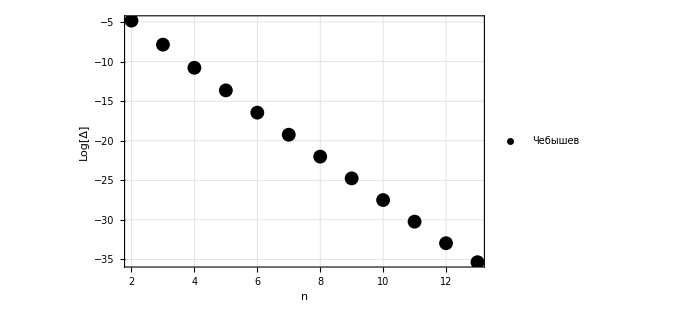

```mathematica
func2[x_]:=Log[x]/(√((3-x)*(x-1)));
b=3;
a=1;
knots2=Table[Table[Cos[((2*i-1)*Pi)/(2*n)]//N,{i,1,n,1}],{n,2,15,1}];
values=Table[2/2*Pi/n*Sum[Log[2/2* knots2[[n-1]][[i]]+4/2],{i,1,n,1}],{n,2,15,1}]
Pi*Log[(2+√3)/2]//N
delta=Table[{i+1,Log[values[[i]]-Pi*Log[(2+√3)/2]//N]},{i,1,14,1}];
Show[ListPlot[delta,
PlotStyle->{Red,Blue,Black},PlotLegends->Placed[
{Style["Чебышев",20,Black,FontFamily->"Cambria"]},Right]],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["n",20,Black,FontFamily->"Cambria"],Style["Log[Δ]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,
PlotRange->{Automatic,Automatic}
]
```

```mathematica
func4[x_]:=E^x*E^(-x^2);
Ln=Table[Simplify[E^x/(n!)*D[E^-x*x^n,{x,n }]]//N,{n,2,6+10,1}];
Length[Ln];
knots3=Table[
Solve[Ln[[n]]==0,x]
,{n,1,4+10,1}];
Length[knots3];
wn3=Table[
Table[knots3[[n]][[i]][[1]][[2]]/((n+1+1)^2*(Ln[[n+1]])^2/.{x->knots3[[n]][[i]][[1]][[2]]}),
{i,1,Length[knots3[[n]]],1}],
{n,1,4+10,1}];
Table[Sum[wn3[[n-1]][[i]]*Sqrt[knots3[[n-1]][[i]][[1]][[2]]],{i,1,n,1}],{n,2,5,1}]
√Pi/2//N
(*The second method*)
Table[Sum[wn3[[n-1]][[i]]*func4[knots3[[n-1]][[i]][[1]][[2]]],{i,1,n,1}],{n,2,5+10,1}]
(*The fourth method*)
√Last[Pi*Table[Sum[wn3[[n-1]][[i]],{i,1,n,1}],{n,2,5+10,1}]]/2
```

{0.92388,0.90644,0.89928,0.895538}

0.886227

{1.08799,0.920904,0.847679,0.855783,0.879146,0.891382,0.892596,0.889466,0.886556,0.885249,0.885196,0.885653,0.886103,0.886351}

0.886227

```mathematica
(*the First method*)
Hrm=Table[Simplify[(-1)^n E^(x^2)*D[E^(-x^2),{x,n }]]//N,{n,1,6,1}];
knots4=Table[
Solve[Hrm[[n]]==0,x],{n,1,5,1}];
wn4=Table[
Table[2^(n-1)*(n)!*√Pi/((n)^2*(Hrm[[n-1]])^2/.{x->knots4[[n]][[i]][[1]][[2]]}),
{i,1,Length[knots4[[n]]],1}],
{n,2,5,1}];
Table[Sum[wn4[[n-1]][[i]],{i,1,n,1}],{n,2,5,1}]/2
```

{0.886227,0.886227,0.886227,0.886227}

```mathematica
(*The third method*)
Func5[dx_]:=Sum[E^(-x^2)*dx//N,{x,0,100,dx}];
(*With[{eps=0.0001},FixedPoint[Function[{dx},Func5[dx]],1,SameTest->(Abs[#1-#2]<eps&)]]*)
I0=Func5[1/1100];
I1=Func5[1/2200];
R=(I1-I0)/(4-1);
Rp=0;
While[Abs[R-Rp]>0.0001,
step=step/2;
I1=Func5[step]//N;
Rp=R;
R=(I1-I0)/(4-1);
I0=I1;
]
I1
```

0.886454